```mathematica
ListPlay[Table[Sin[440 2Pi t],{t,0,2,1/8000}]]
```

-Graphics-

```mathematica
Export["/home/adam/temp.wav",ListPlay[Table[2Sin[100Pi t^2 ],{t,0,4,1/8000}]]]
```

/home/adam/temp.wav

```mathematica
Export["/home/adam/temp.wav",ListPlay[step/@Range[4000],SampleRate->1500]]
```

/home/adam/temp.wav

```mathematica
step[0]=Random[]
```

0.22403

```mathematica
Clear[step]
r=3;
step[0]=Random[]
step[i_]:=step[i]=(10/3+i/300000) step[i-1](1-step[i-1])
Export["/home/adam/temp2.wav",ListPlay[step[Floor[#]]&/@Range[0,200000,.5]]]
```

0.704575

/home/adam/temp2.wav

```mathematica
step/
```

```mathematica
Table[(-1)^(8000t),{t,0,4,1/8000}]
```

{1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,31887,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1}
 |  |  |  |

```mathematica
Export["/home/adam/temp.wav",ListPlay[Table[2Sin[22Pi(t-(1/Pi)Sin[Pi t]) ],{t,0,2,1/1600}]]]
```

```mathematica
Export["/home/adam/temp.wav",ListPlay[Table[-1]]
```

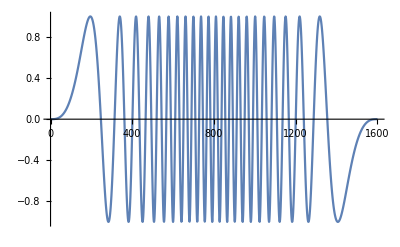

```mathematica
ListLinePlot[Table[Sin[22Pi(t-(1/Pi)Sin[Pi t]) ],{t,0,2,1/800}]]
```

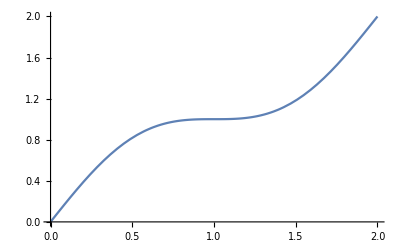

```mathematica
Plot[(t+(1/Pi)Sin[Pi t]),{t,0,2}]
```